# EIWL Sections 41,42

## Section 41

```mathematica
Cases[IntegerDigits[Range[100]^2],{___,x_,x_,___}]
```

{{1,0,0},{1,4,4},{2,2,5},{4,0,0},{4,4,1},{9,0,0},{1,1,5,6},{1,2,2,5},{1,4,4,4},{1,6,0,0},{2,1,1,6},{2,2,0,9},{2,5,0,0},{3,3,6,4},{3,6,0,0},{3,8,4,4},{4,2,2,5},{4,4,8,9},{4,9,0,0},{5,7,7,6},{6,4,0,0},{6,8,8,9},{7,2,2,5},{7,7,4,4},{8,1,0,0},{8,8,3,6},{1,0,0,0,0}}

```mathematica
Cases[Characters[RomanNumeral[Range[100]]],{___,"L",___,"I",___,"X"}]
```

{{X,L,I,X},{L,I,X},{L,X,I,X},{L,X,X,I,X},{L,X,X,X,I,X}}

```mathematica
Cases[Partition[TextWords[WikipediaData["alliteration"]],2,1],{a_,b_}/;StringTake[a,1]==StringTake[b,1]]
```

{{or,of},{as,a},{Peter,Piper},{pickled,peppers},{Irish,It},{as,an},{ideas,in},{Icelandic,It},{cartoon,characters},{the,term},{identical,initial},{several,special},{as,alliteration},{stressed,syllables},{as,an},{lazy,languid},{languid,line},{as,alliteration},{be,because},{such,syllables},{syllables,start},{consonant,clusters},{sp,st},{consonant,clusters},{s,sound},{consonant,cluster},{cluster,can},{with,words},{consonant,cluster},{s,such},{sp,st},{Walt,Whitman},{Splendid,Silent},{Silent,Sun},{consonant,clusters},{sp,st},{spit,sting},{stick,skin},{consonant,clusters},{s,seems},{same,source},{consonant,clusters},{to,the},{the,two},{identical,in},{at,any},{home,hot},{as,a},{stressed,syllable},{humble,house},{potential,power},{power,play},{play,picture},{picture,perfect},{money,matters},{rocky,road},{quick,question},{Peter,Piper},{pickled,peppers},{of,outside},{same,sound},{of,outside},{to,the},{brown,blazers},{in,its},{Poetry,Poets},{can,call},{splendid,silent},{silent,sun},{Walt,Whitman},{Splendid,Silent},{Silent,Sun},{wondered,what},{his,horse},{also,add},{to,the},{harsh,hard},{they,than},{slippered,sleep},{lean,lithe},{fleet,flown},{E.,E.},{heaped,heartbreak},{fire,forthrightly},{Chappell,Chestnuts},{finally,finding},{Finch,Fresh-firecoal},{plotted,pieced},{fold,fallow},{height,hangs},{hangs,his},{who,wanders},{barred,by},{Who,Wanders},{I,In},{sat,silent},{We,Were},{swart,ship},{with,weeping},{out,onward},{out,of},{to,the},{sun,sword},{axe,angles},{hell's,handiwork},{silken,sad},{breeze,blew},{foam,flew},{furrow,followed},{followed,free},{stood,still},{churlish,chiding},{winter's,wind},{brown,below},{harvests,hang},{heavy,head},{Brent,Bernard},{who,watch},{watch,with},{with,wild},{wild,wonder},{wide,window},{beautiful,birds},{birds,begin},{bountiful,birdseed},{Thurston,Three},{grey,geese},{Grey,Geese},{Betty,Botter},{butter,but},{she,said},{butter's,bitter},{it,in},{make,my},{batter,bitter},{bitter,but},{better,butter},{make,my},{bitter,batter},{batter,better},{the,tongue-twister},{Betty,Botter},{Peter,Piper},{pickled,peppers},{Peter,Piper},{pickled,peppers},{pickled,peppers},{Peter,Piper},{Helplessly,Hoping},{throughout,the},{stand,still},{stood,still},{Fairyland,Fanfare},{legend,live},{live,life},{all,alone},{to,the},{lunar,lure},{lacking,lustre},{late,last},{as,an},{an,artistic},{emotional,effect},{any,attitude},{is,in},{as,an},{which,we},{our,only},{of,our},{our,own},{but,by},{today,that},{that,the},{truths,that},{is,inextricably},{to,the},{itself,is},{testimony,to},{to,the},{have,had},{because,brave},{freedom's,front},{Ronald,Reagan},{Vietnam,Veterans},{new,nation},{to,the},{portae,proficiscere},{blonde,bad-built},{bad-built,butch},{butch,body},{and,adds},{adds,an},{an,alliterative},{Μάρθα,Μάρθα},{Martha,Martha},{Martha,Martha},{House,Handbook},{Modern,Memory},{to,the},{Some,Suggestive},{4,438},{438,45},{E,E},{55,5},{388,390},{Indolence,ISBN},{R,R},{alliteration,and},{and,alliterative},{alliterations,and}}

```mathematica
Grid[FixedPointList[(#/. {x___,b_,a_,y___}/;b>a->{x,a,b,y})&,{4,5,1,3,2}]]
```

4 | 5 | 1 | 3 | 2
4 | 1 | 5 | 3 | 2
1 | 4 | 5 | 3 | 2
1 | 4 | 3 | 5 | 2
1 | 3 | 4 | 5 | 2
1 | 3 | 4 | 2 | 5
1 | 3 | 2 | 4 | 5
1 | 2 | 3 | 4 | 5
1 | 2 | 3 | 4 | 5

```mathematica
ArrayPlot[Transpose[FixedPointList[(#/. {x___,b_,a_,y___}/;b>a->{x,a,b,y})&,RandomInteger[10,50]]]]
```

-Graphics-

```mathematica
f[a_]:=(a+2/a)/2
```

```mathematica
FixedPointList[(#+2/#)/2&,1.0]
```

{1.,1.5,1.41667,1.41422,1.41421,1.41421,1.41421}

```mathematica
FixedPointList[(#/. {a_,b_}/;b!=0->{b,Mod[a,b]})&,{12345,54321}]
```

{{12345,54321},{54321,12345},{12345,4941},{4941,2463},{2463,15},{15,3},{3,0},{3,0}}

```mathematica
FixedPointList[#/.{s[x_][y_][z_]->x[z][y[z]],k[x_][y_]->x}&,s[s][k][s[s[s]][s]][s]]
```

{s[s][k][s[s[s]][s]][s],s[s[s[s]][s]][k[s[s[s]][s]]][s],s[s[s]][s][s][k[s[s[s]][s]][s]],s[s][s][s[s]][s[s[s]][s]],s[s[s]][s[s[s]]][s[s[s]][s]],s[s][s[s[s]][s]][s[s[s]][s[s[s]][s]]],s[s[s[s]][s[s[s]][s]]][s[s[s]][s][s[s[s]][s[s[s]][s]]]],s[s[s[s]][s[s[s]][s]]][s[s][s[s[s]][s[s[s]][s]]][s[s[s[s]][s[s[s]][s]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s]][s[s[s]][s]][s[s[s[s]][s[s[s]][s]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s][s[s[s[s]][s[s[s]][s]]]][s[s[s]][s][s[s[s[s]][s[s[s]][s]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s[s]][s][s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s]][s][s[s[s[s]][s[s[s]][s]]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s][s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s]][s[s[s]][s]]]]]][s[s[s[s]][s[s[s]][s]]][s[s][s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s]][s[s[s]][s]]]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]]]]],s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]][s[s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s[s]][s[s[s]][s]]]]][s[s[s[s]][s[s[s]][s]]][s[s[s[s[s]][s[s[s]][s]]]]]]]]]]}

```mathematica
IntegerDigits[100!]/. {x___,0..}->{x}
```

{9,3,3,2,6,2,1,5,4,4,3,9,4,4,1,5,2,6,8,1,6,9,9,2,3,8,8,5,6,2,6,6,7,0,0,4,9,0,7,1,5,9,6,8,2,6,4,3,8,1,6,2,1,4,6,8,5,9,2,9,6,3,8,9,5,2,1,7,5,9,9,9,9,3,2,2,9,9,1,5,6,0,8,9,4,1,4,6,3,9,7,6,1,5,6,5,1,8,2,8,6,2,5,3,6,9,7,9,2,0,8,2,7,2,2,3,7,5,8,2,5,1,1,8,5,2,1,0,9,1,6,8,6,4}

```mathematica
newList[{x_,y_,everythingElse___}]:=Switch[x,1,Join[{everythingElse},{0,1}],0,Join[{everythingElse},{1,0,0}]]
Length/@NestList[newList,{1,0},200]
```

{2,2,3,3,4,4,5,6,6,7,8,9,9,10,11,11,12,12,13,13,14,14,15,16,16,17,17,18,19,19,20,21,22,22,23,23,24,24,25,25,26,26,27,28,29,29,30,30,31,32,32,33,33,34,35,35,36,37,37,38,38,39,40,40,41,42,43,43,44,44,45,45,46,46,47,47,48,48,49,50,50,51,52,53,53,54,55,55,56,56,57,58,58,59,59,60,61,61,62,62,63,64,64,65,66,67,67,68,69,69,70,70,71,71,72,72,73,74,74,75,76,77,77,78,78,79,79,80,80,81,82,82,83,84,85,85,86,87,87,88,88,89,89,90,90,91,92,92,93,93,94,95,95,96,97,98,98,99,100,100,101,101,102,103,103,104,104,105,106,106,107,108,109,109,110,111,111,112,112,113,113,114,114,115,116,116,117,117,118,119,119,120,121,122,122,123,123,124,124,125,125}

```mathematica
newnewList[{x_,y_,everythingElse___}]:=Switch[x,1,Join[{everythingElse},{0}],0,Join[{everythingElse},{2,1}],2,Join[{everythingElse},{0,2,1,2}]]
```

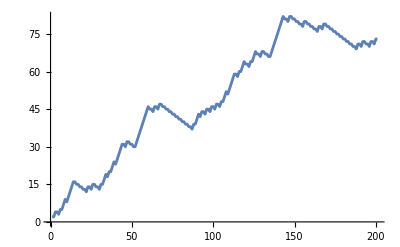

```mathematica
ListLinePlot[Length/@NestList[newnewList,{0,0},200]]
```

## Section 42

```mathematica
StringReplace["1 2 3 4",{" "->"---"}]
```

1---2---3---4

```mathematica
StringCases[WikipediaData["computers"],{DigitCharacter~~DigitCharacter~~DigitCharacter~~DigitCharacter}]
```

{1940,1950,1970,1613,1943,1640,1897,1945,1937,2400,1901,1235,1000,1620,1630,1770,1831,1835,4000,1872,1876,1920,1890,1901,1822,1833,1888,1906,1914,1920,1872,1876,1927,1950,1950,1937,1938,1939,1941,2000,1950,1941,1930,1934,1942,1943,1943,1944,5000,1943,1945,1936,1936,1945,1945,1945,1948,1998,1951,1953,1957,1947,1949,1951,1925,1947,1948,1955,1953,1955,1955,1955,1960,1952,1958,1958,1959,1959,1962,1964,1967,1968,4004,1970,1945,5100,2000,2000,1970,1357,1357,2468,1595,2016,6502,6510,1947,1950,1970,1990}

```mathematica
Grid[Table[StringTemplate["`i`+`j`"][<|"i"->i,"j"->j|>],{i,1,9},{j,1,9}]]
```

1+1 | 1+2 | 1+3 | 1+4 | 1+5 | 1+6 | 1+7 | 1+8 | 1+9
2+1 | 2+2 | 2+3 | 2+4 | 2+5 | 2+6 | 2+7 | 2+8 | 2+9
3+1 | 3+2 | 3+3 | 3+4 | 3+5 | 3+6 | 3+7 | 3+8 | 3+9
4+1 | 4+2 | 4+3 | 4+4 | 4+5 | 4+6 | 4+7 | 4+8 | 4+9
5+1 | 5+2 | 5+3 | 5+4 | 5+5 | 5+6 | 5+7 | 5+8 | 5+9
6+1 | 6+2 | 6+3 | 6+4 | 6+5 | 6+6 | 6+7 | 6+8 | 6+9
7+1 | 7+2 | 7+3 | 7+4 | 7+5 | 7+6 | 7+7 | 7+8 | 7+9
8+1 | 8+2 | 8+3 | 8+4 | 8+5 | 8+6 | 8+7 | 8+8 | 8+9
9+1 | 9+2 | 9+3 | 9+4 | 9+5 | 9+6 | 9+7 | 9+8 | 9+9

```mathematica
Cases[Characters[IntegerName[Range[50]]],{___,"i",___,"e",___}]
```

{{f,i,v,e},{n,i,n,e},{t,h,i,r,t,e,e,n},{f,i,f,t,e,e,n},{s,i,x,t,e,e,n},{e,i,g,h,t,e,e,n},{n,i,n,e,t,e,e,n},{t,w,e,n,t,y,-,f,i,v,e},{t,w,e,n,t,y,-,n,i,n,e},{t,h,i,r,t,y,-,o,n,e},{t,h,i,r,t,y,-,t,h,r,e,e},{t,h,i,r,t,y,-,f,i,v,e},{t,h,i,r,t,y,-,s,e,v,e,n},{t,h,i,r,t,y,-,e,i,g,h,t},{t,h,i,r,t,y,-,n,i,n,e},{f,o,r,t,y,-,f,i,v,e},{f,o,r,t,y,-,n,i,n,e}}

```mathematica
ToUpperCase[StringCases[TextSentences[WikipediaData["computers"]][[1]],{Whitespace~~LetterCharacter~~LetterCharacter~~Whitespace}]]
```

{ IS , BE , TO , OF , OR }

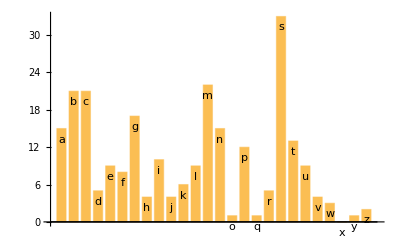

```mathematica
BarChart[Count[StringTake[CommonName[],1],#]&/@ToUpperCase[Alphabet[]],ChartLabels->Placed[Alphabet[],Top]]
```

```mathematica
Grid[Table[StringTemplate["``^``=``"][i,j,i^j],{i,5},{j,5}]]
```

1^1=1 | 1^2=1 | 1^3=1 | 1^4=1 | 1^5=1
2^1=2 | 2^2=4 | 2^3=8 | 2^4=16 | 2^5=32
3^1=3 | 3^2=9 | 3^3=27 | 3^4=81 | 3^5=243
4^1=4 | 4^2=16 | 4^3=64 | 4^4=256 | 4^5=1024
5^1=5 | 5^2=25 | 5^3=125 | 5^4=625 | 5^5=3125